```mathematica
(* Note: I eventually abandoned this workbook in favour of simply integrating the Schrodinger equation through the experiment as opposed to trying to find the stark states via the eigenvalue problem. This worksheet still solves for the Stark states but is unable to order the eigenvectors so that I can map a HFS state directly to its corresponding Stark state. For quick calculations of Stark energies or mixing ratios, this sheet works just fine. Note also that this sheet was a rough/working draft of DCStark. *)
(* This worksheet is in S.I. units *)
(* The Hamiltonian matrices are missing a factor of h (not h-bar) just to make the computations *)(* easier to see (fewer numbers after the decimal) *)
ClearAll["Global`*"]
$Assumptions={aμ>0,r>=0,θ>=0,ϕ>=0,Element[{r,θ,ϕ,aμ},Reals]};
P[n_,l_,r_,Z_]:=Sqrt[Factorial[n-l-1]*Z/(n^2*Factorial[n+l]^3*aμ)]*(2*Z*r/(n*aμ))^(l+1)*Exp[-Z*r/(n*aμ)]*Factorial[n+l]^2*Sum[(-2*Z*r/(n*aμ))^k/(Factorial[k]*Factorial[n-l-1-k]*Factorial[2*l+1+k]),{k,0,n-l-1}];
CartesianWaveFunction[n_,l_,m_,r_,θ_,ϕ_,Z_]:=P[n,l,r,Z]*SphericalHarmonicY[l,m,θ,ϕ]/(r);
DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\radial.mx"]
DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\angularx.mx"]
DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\angulary.mx"]
DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\angularz.mx"]
```

```mathematica
rbar[n_,l_,m_,np_,lp_,mp_]:={radialmatrix⟦n,l+1,np,lp+1⟧*angularxmatrix⟦l+1,Abs[m]+1,If[m≥0,2,1],lp+1,Abs[mp]+1,If[mp≥0,2,1]⟧,radialmatrix⟦n,l+1,np,lp+1⟧*angularymatrix⟦l+1,Abs[m]+1,If[m≥0,2,1],lp+1,Abs[mp]+1,If[mp≥0,2,1]⟧,radialmatrix⟦n,l+1,np,lp+1⟧*angularzmatrix⟦l+1,Abs[m]+1,If[m≥0,2,1],lp+1,Abs[mp]+1,If[mp≥0,2,1]⟧};
(*rbar[n_,l_,m_,np_,lp_,mp_]:={Integrate[Conjugate[CartesianWaveFunction[np,lp,mp,r,θ,ϕ,1]]*r*Sin[θ]*Cos[ϕ]*CartesianWaveFunction[n,l,m,r,θ,ϕ,1]*r^2*Sin[θ],{r,0,Infinity},{θ,0,π},{ϕ,0,2*π}],Integrate[Conjugate[CartesianWaveFunction[np,lp,mp,r,θ,ϕ,1]]*r*Sin[θ]*Sin[ϕ]*CartesianWaveFunction[n,l,m,r,θ,ϕ,1]*r^2*Sin[θ],{r,0,Infinity},{θ,0,π},{ϕ,0,2*π}],Integrate[Conjugate[CartesianWaveFunction[np,lp,mp,r,θ,ϕ,1]]*r*Cos[θ]*CartesianWaveFunction[n,l,m,r,θ,ϕ,1]*r^2*Sin[θ],{r,0,Infinity},{θ,0,π},{ϕ,0,2*π}]};*)
```

```mathematica
rb=rbar[2,1,0,1,0,0];
mpCODATA=1672621898*10^-36;
meCODATA=910938356*10^-39;
μ=meCODATA*mpCODATA/(meCODATA+mpCODATA);
a0CODATA=52917721067*10^-21;
aμ=a0CODATA*meCODATA/μ;
RyCODATA=Rationalize[10973731568508*10^-6];
αCODATA=Rationalize[72973525664*10^-33];
eCODATA=Rationalize[16021766208*10^-29];
hbarCODATA=Rationalize[1054571800*10^-43];
cCODATA =299792458;
τ0=3*hbarCODATA*2^5/(2*αCODATA^5*μ*cCODATA^2)*(meCODATA+mpCODATA)/(meCODATA+mpCODATA);
const=Rationalize[1.6*((1-1/4)^3*Dot[Conjugate[rb],rb]/(aμ^2))]
N[const]
(* The output here should be 4096/10935 and 0.374577 *)
```

4096/10935

0.374577

```mathematica
m=0;
lt[n_,l_]:=const/Sum[Sum[Sum[rb=rbar[n,l,m,np,lp,mp];(1/np^2-1/n^2)^3*Dot[Conjugate[rb],rb]/aμ^2,{mp,Max[m-1,-lp],Min[m+1,lp]}],{np,Max[lp+1,1],n-1}],{lp,{Max[l-1,0],l+1}}]
gamma[n_,l_]:=Sum[Sum[Sum[rb=rbar[n,l,m,np,lp,mp];(1/np^2-1/n^2)^3*Dot[Conjugate[rb],rb]/aμ^2,{mp,Max[m-1,-lp],Min[m+1,lp]}],{np,Max[lp+1,1],n-1}],{lp,{Max[l-1,0],l+1}}]/const
```

```mathematica
(* Only run this if calculation of gammas is desired. *)
gammas=Table[Table[gamma[n,l],{l,0,n-1}],{n,1,20}]
(*Export["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\gammas.dat",gammas]*)
```

```mathematica
i=1/2;
s=1/2;
HydrogenWaveFunction[{n_,l_,j_,f_,mf_,r_,θ_,ϕ_,Z_}]:=(hwf={};Do[thisOne=Flatten[{Sqrt[2*f+1]*(-1)^(j+i+mf)*ThreeJSymbol[{j,mj},{i,mi},{f,-mf}],Sqrt[2*j+1]*(-1)^(l+s+mj)*ThreeJSymbol[{l,ml},{s,ms},{j,-mj}],0,l,ml,s,ms,i,mi}];thisOne={thisOne[[1]]*thisOne[[2]],thisOne[[3]],thisOne[[4;;5]],thisOne[[6;;9]]};hwf=If[thisOne[[1]]≠0,Append[hwf,thisOne],hwf],{ml,-l,l},{ms,-s,s},{mj,-j,j},{mi,-i,i}];hwf)
(*HydrogenWaveFunction[{n_,l_,j_,f_,mf_,r_,θ_,ϕ_,Z_}]:=(hwf={};Do[thisOne=Flatten[{Sqrt[2*f+1]*(-1)^(j+i+mf)*ThreeJSymbol[{j,mj},{i,mi},{f,-mf}],Sqrt[2*j+1]*(-1)^(l+s+mj)*ThreeJSymbol[{l,ml},{s,ms},{j,-mj}],CartesianWaveFunction[n,l,ml,r,θ,ϕ,Z],l,ml,s,ms,i,mi}];thisOne={thisOne[[1]]*thisOne[[2]],thisOne[[3]],thisOne[[4;;5]],thisOne[[6;;9]]};hwf=If[thisOne[[1]]≠0,Append[hwf,thisOne],hwf],{ml,-l,l},{ms,-s,s},{mj,-j,j},{mi,-i,i}];hwf)
xEV[qnums1_,qnums2_]:=(hwf1=HydrogenWaveFunction[qnums1];hwf2=HydrogenWaveFunction[qnums2];ev=0;Do[Do[If[And[Or[KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]+1]==1,KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]-1]==1],KroneckerDelta[hwf1[[j,4]],hwf2[[k,4]]]==1],ev=ev+eCODATA*Integrate[Conjugate[hwf1⟦j,1⟧*hwf1⟦j,2⟧]*qnums1⟦6⟧*Sin[qnums1⟦7⟧]*Cos[qnums1⟦8⟧]*hwf2⟦k,1⟧*hwf2⟦k,2⟧*qnums1⟦6⟧^2*Sin[qnums1⟦7⟧],{qnums1⟦6⟧,0,Infinity},{qnums1⟦7⟧,0,π},{qnums1⟦8⟧,0,2*π}]/(2*π*hbarCODATA)],{j,Length[hwf1]}],{k,Length[hwf2]}];ev)
yEV[qnums1_,qnums2_]:=(hwf1=HydrogenWaveFunction[qnums1];hwf2=HydrogenWaveFunction[qnums2];ev=0;Do[Do[If[And[Or[KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]+1]==1,KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]-1]==1],KroneckerDelta[hwf1[[j,4]],hwf2[[k,4]]]==1],ev=ev+eCODATA*Integrate[Conjugate[hwf1⟦j,1⟧*hwf1⟦j,2⟧]*qnums1⟦6⟧*Sin[qnums1⟦7⟧]*Sin[qnums1⟦8⟧]*hwf2⟦k,1⟧*hwf2⟦k,2⟧*qnums1⟦6⟧^2*Sin[qnums1⟦7⟧],{qnums1⟦6⟧,0,Infinity},{qnums1⟦7⟧,0,π},{qnums1⟦8⟧,0,2*π}]/(2*π*hbarCODATA)],{j,Length[hwf1]}],{k,Length[hwf2]}];ev)
zEV[qnums1_,qnums2_]:=(hwf1=HydrogenWaveFunction[qnums1];hwf2=HydrogenWaveFunction[qnums2];ev=0;Do[Do[If[And[Or[KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]+1]==1,KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]-1]==1],KroneckerDelta[hwf1[[j,3,2]]-hwf2[[k,3,2]]]==1,KroneckerDelta[hwf1[[j,4]],hwf2[[k,4]]]==1],ev=ev+eCODATA*Integrate[Conjugate[hwf1⟦j,1⟧*hwf1⟦j,2⟧]*qnums1⟦6⟧*Cos[qnums1⟦7⟧]*hwf2⟦k,1⟧*hwf2⟦k,2⟧*qnums1⟦6⟧^2*Sin[qnums1⟦7⟧],{qnums1⟦6⟧,0,Infinity},{qnums1⟦7⟧,0,π},{qnums1⟦8⟧,0,2*π}]/(2*π*hbarCODATA)],{j,Length[hwf1]}],{k,Length[hwf2]}];ev)*)
xEV[qnums1_,qnums2_]:=(hwf1=HydrogenWaveFunction[qnums1];hwf2=HydrogenWaveFunction[qnums2];ev=0;Do[Do[If[And[Or[KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]+1]==1,KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]-1]==1],KroneckerDelta[hwf1[[j,4]],hwf2[[k,4]]]==1],ev=ev+eCODATA*Conjugate[hwf1⟦j,1⟧]*hwf2⟦k,1⟧*radialmatrix⟦qnums1⟦1⟧,hwf1⟦j,3,1⟧+1,qnums2⟦1⟧,hwf2⟦k,3,1⟧+1⟧*angularxmatrix⟦hwf1⟦j,3,1⟧+1,Abs[hwf1⟦j,3,2⟧]+1,If[hwf1⟦j,3,2⟧≥0,2,1],hwf2⟦k,3,1⟧+1,Abs[hwf2⟦k,3,2⟧]+1,If[hwf2⟦k,3,2⟧≥0,2,1]⟧/(2*π*hbarCODATA)],{j,Length[hwf1]}],{k,Length[hwf2]}];ev)
yEV[qnums1_,qnums2_]:=(hwf1=HydrogenWaveFunction[qnums1];hwf2=HydrogenWaveFunction[qnums2];ev=0;Do[Do[If[And[Or[KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]+1]==1,KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]-1]==1],KroneckerDelta[hwf1[[j,4]],hwf2[[k,4]]]==1],ev=ev+eCODATA*Conjugate[hwf1⟦j,1⟧]*hwf2⟦k,1⟧*radialmatrix⟦qnums1⟦1⟧,hwf1⟦j,3,1⟧+1,qnums2⟦1⟧,hwf2⟦k,3,1⟧+1⟧*angularymatrix⟦hwf1⟦j,3,1⟧+1,Abs[hwf1⟦j,3,2⟧]+1,If[hwf1⟦j,3,2⟧≥0,2,1],hwf2⟦k,3,1⟧+1,Abs[hwf2⟦k,3,2⟧]+1,If[hwf2⟦k,3,2⟧≥0,2,1]⟧/(2*π*hbarCODATA)],{j,Length[hwf1]}],{k,Length[hwf2]}];ev)
zEV[qnums1_,qnums2_]:=(hwf1=HydrogenWaveFunction[qnums1];hwf2=HydrogenWaveFunction[qnums2];ev=0;Do[Do[If[And[Or[KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]+1]==1,KroneckerDelta[hwf1[[j,3,1]]-hwf2[[k,3,1]]-1]==1],KroneckerDelta[hwf1[[j,3,2]]-hwf2[[k,3,2]]]==1,KroneckerDelta[hwf1[[j,4]],hwf2[[k,4]]]==1],ev=ev+eCODATA*Conjugate[hwf1⟦j,1⟧]*hwf2⟦k,1⟧*radialmatrix⟦qnums1⟦1⟧,hwf1⟦j,3,1⟧+1,qnums2⟦1⟧,hwf2⟦k,3,1⟧+1⟧*angularzmatrix⟦hwf1⟦j,3,1⟧+1,Abs[hwf1⟦j,3,2⟧]+1,If[hwf1⟦j,3,2⟧≥0,2,1],hwf2⟦k,3,1⟧+1,Abs[hwf2⟦k,3,2⟧]+1,If[hwf2⟦k,3,2⟧≥0,2,1]⟧/(2*π*hbarCODATA)],{j,Length[hwf1]}],{k,Length[hwf2]}];ev)
Quiet[HydrogenWaveFunction[{1,0,1/2,0,0,r,θ,ϕ,1}]];
Quiet[zEV[{2,0,1/2,0,0,r,θ,ϕ,1},{2,1,1/2,1,0,r,θ,ϕ,1}]]//N
```

22174.4

```mathematica
rbarhfs[qnums1_,qnums2_]:={xEV[qnums1,qnums2],yEV[qnums1,qnums2],zEV[qnums1,qnums2]};
```

```mathematica
lst=Flatten[Table[{n,l,j,f,mf},{n,3,3},{l,0,n-1},{j,Max[l-1/2,1/2],l+1/2},{f,Max[j-1/2,0],j+1/2},{mf,-f,f}],4];
Length[lst]
```

36

```mathematica
xmtx = ConstantArray[0,{Length[lst],Length[lst]}];
ymtx = ConstantArray[0,{Length[lst],Length[lst]}];
zmtx = ConstantArray[0,{Length[lst],Length[lst]}];
Timing[Do[Do[xmtx[[k,j]]=xEV[Join[lst[[j,;;]],{r,θ,ϕ,1}],Join[lst[[k,;;]],{r,θ,ϕ,1}]],{j,k,Length[lst]}],{k,1,Length[lst]}];
Do[Do[xmtx[[j,k]]=Conjugate[xmtx[[k,j]]],{j,k,Length[lst]}],{k,1,Length[lst]}]]
Timing[Do[Do[ymtx[[k,j]]=yEV[Join[lst[[j,;;]],{r,θ,ϕ,1}],Join[lst[[k,;;]],{r,θ,ϕ,1}]],{j,k,Length[lst]}],{k,1,Length[lst]}];
Do[Do[ymtx[[j,k]]=Conjugate[ymtx[[k,j]]],{j,k,Length[lst]}],{k,1,Length[lst]}]]
Timing[Do[Do[zmtx[[k,j]]=zEV[Join[lst[[j,;;]],{r,θ,ϕ,1}],Join[lst[[k,;;]],{r,θ,ϕ,1}]],{j,k,Length[lst]}],{k,1,Length[lst]}];
Do[Do[zmtx[[j,k]]=Conjugate[zmtx[[k,j]]],{j,k,Length[lst]}],{k,1,Length[lst]}]]
xmtx//MatrixForm
ymtx//MatrixForm
zmtx//MatrixForm
(*Export["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n6list.dat",lst]
Export["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n6xmtrx.dat",xmtx]
Export["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n6ymtrx.dat",ymtx]
Export["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n6zmtrx.dat",zmtx]*)
```

C:\Users\travis\Google Drive\Travis Code\Simulations\DCStark\n6list.dat

C:\Users\travis\Google Drive\Travis Code\Simulations\DCStark\n6xmtrx.dat

C:\Users\travis\Google Drive\Travis Code\Simulations\DCStark\n6ymtrx.dat

C:\Users\travis\Google Drive\Travis Code\Simulations\DCStark\n6zmtrx.dat

```mathematica
(* The energies file is simply a list of n,j,l,f,E-E_(n,S,f=0) 
The gammas file is a table of values of 1/lifetime for each n,l state. The indices of the table are n and l. If you want to compute the Hamiltonian for the matrix of n states, look in the energies file and find the index or browse the array here.
*)
energies=Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\FSHFSEnergies.dat","Table"];
numn=Max[energies[[;;,1]]];
numl=Max[energies[[;;,3]]];
energytable=ConstantArray[0,{20,20,2,2}];
Do[energytable[[energies[[i,1]],energies[[i,3]]+1,ToExpression[energies[[i,2]]]+1/2-energies[[i,3]]+1,energies[[i,4]]+1/2-ToExpression[energies[[i,2]]]+1]]=energies[[i,5]],{i,Length[energies]}];
gammas=Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\gammas.dat","Table"];
```

```mathematica
(* Create the diagonal elements of the matrix from the energies and precalculated lifetimes/gamma values*)
(* In the gammas.dat file, the gamma values are in ns^-1 *)
Clear[Efield];
thisn=5; (* Specify the n for which the eigenvalue problem should be solved. *)
fielddir="z"; (* Specify the direction of the perturbing electric field. *)
complexEnergy=False; (* If a calculation with the complex energies is desired, this should be set to True. *)
prec=20;
additive=1; (* how many THz to add to the energies in order to get rid of degeneracy and thus inadvertant mixing *)
(* MAKE SURE "additive" is an integer! *)
$MaxPrecision=Infinity;
(* To the energies, we add mf*additive *)
dgelements=Flatten[Table[Table[Table[Table[Table[energytable[[n,l+1,j+1/2-l+1,f+1/2-j+1]]-If[complexEnergy==True,ⅈ*ToExpression[gammas[[n,l+1]]]*10^9,0],{mf,-f,f}],{f,j-1/2,j+1/2}],{j,Max[l-1/2,1/2],l+1/2}],{l,0,n-1}],{n,thisn,thisn}]];
hmtx=DiagonalMatrix[dgelements];
(* If calculating the Stark states for a matrix, import it here. *)(* I plan to just save the files for eigenvalues/eigenvectors as a function of Efield later on. *)lst=Flatten[Table[{n,l,j,f,mf},{n,thisn,thisn},{l,0,n-1},{j,Max[l-1/2,1/2],l+1/2},{f,Max[j-1/2,0],j+1/2},{mf,-f,f}],4];
Length[lst]
mtx=Import["C:\\Users\\travis\\Documents\\Simulations\\DCStark\\n"<>ToString[thisn]<>fielddir<>"mtrx.dat","Table"];
mtx=ToExpression[mtx];
(* Extra gamma values for the 2s state (doesn't actually have an infinite lifetime). *)
(* This has quite a large effect on how many 2S atoms survive within an electric field. *)
twosgammas=ConstantArray[0,{16,16}];
twosgammas[[1,1]]=-ⅈ*10000/32;
twosgammas[[2,2]]=-ⅈ*10000/32;
twosgammas[[3,3]]=-ⅈ*10000/32;
twosgammas[[4,4]]=-ⅈ*10000/32;
newmtx[Efield_]:=(matrix=Efield*100*mtx+hmtx+If[thisn==2,twosgammas,0*IdentityMatrix[Length[hmtx]]];
matrix)
valsvecs[Efield_]:=Eigensystem[newmtx[Efield]];
totalstates[n_]:=4*n^2; (* Total number of mf states in a particular n *)
```

100

```mathematica
(* Function to extract block matrices from the diagonal of a block diagonal matrix *)
extractBDM[mat_?MatrixQ]:=(stuff=ComponentMeasurements[Image[MorphologicalTransform[Unitize[mat],"BoundingBoxes"]],"Mask",CornerNeighbors->False];
a=Pick[mat,#,1]& /@ stuff⟦;;,2⟧;
posis=Table[If[Length@Position[Normal@stuff⟦j,2,k⟧,1]>0,k,{}],{j,Length[a]},{k,Length[mat]}];
posis=Delete[posis,Position[posis,{}]⟦;;⟧];
a=Delete[a,Position[a,{}]⟦;;⟧];
Table[{Min[posis⟦j⟧],Max[posis⟦j⟧],a⟦j⟧},{j,Length[a]}])
```

```mathematica
(* Here I construct the F_x, F_y, and F_z matrices. The problem with simply diagonalizing the perturbed Hamiltonian is that in all cases, there are still degenerate states. If there are degenerate states, the eigenvectors of those states are ambiguous. For example, if there are four total states and two of those eigenstates are degenerate, then when solving for the eigenstates there are 2 equations and 4 unknowns. This means there are two variables remaining that determine the degenerate eigenstates. The mathematics allows for those two variables to take on any values before being normalized, so long as the two eigenstates are orthonormal. This leads to situations in which, for instance, an m=-1 state gets mixed with an m=1 state in a
z-directional field (the m=1,-1 states are degenerate and are mathematically allowed to mix). However, the physics puts constraints on these eigenvectors and gives us the missing symmetry in order to uniquely determine the eigenstates. *)
fzmtx=DiagonalMatrix[Table[lst⟦j,5⟧,{j,Length[lst]}]];
(* These functions calculate matrix elements as <wf1|f+|wf2> and <wf1|f-|wf2> *)
fplus[wf1_,wf2_]:=(f=wf2⟦4⟧;mf=wf2⟦5⟧;Sqrt[f*(f+1)-mf*(mf+1)]*If[wf2⟦4⟧>wf2⟦5⟧,If[wf1==Append[wf2⟦1;;4⟧,wf2⟦5⟧+1],1,0],0]);
fminus[wf1_,wf2_]:=(f=wf2⟦4⟧;mf=wf2⟦5⟧;Sqrt[f*(f+1)-mf*(mf-1)]*If[-wf2⟦4⟧<wf2⟦5⟧,If[wf1==Append[wf2⟦1;;4⟧,wf2⟦5⟧-1],1,0],0]);
fplusmatrix=Table[fplus[lst⟦k⟧,lst⟦j⟧],{j,Length[lst]},{k,Length[lst]}];
fminusmatrix=Table[fminus[lst⟦k⟧,lst⟦j⟧],{j,Length[lst]},{k,Length[lst]}];
fxmtx=(fplusmatrix+fminusmatrix)/2;
fymtx=(fplusmatrix-fminusmatrix)/(2*ⅈ);
sorteigen[eveclist_,evalslist_]:=(
evecssorted=ConstantArray[0,{Length[eveclist],Length[eveclist⟦1⟧]}]; (* Create empty arrays *)
evalssorted=ConstantArray[0,{Length[evalslist],Length[evalslist⟦1⟧]}];
(* For the first step, sort the eigenvalues/vectors based on the location of the largest coefficient in the eigenvector. *)
Do[
pos=Position[Abs[eveclist⟦1,k⟧],Max[Abs[eveclist⟦1,k⟧]]]⟦1,1⟧;
evecssorted⟦1,pos⟧=eveclist⟦1,k⟧;
evalssorted⟦1,pos⟧=evalslist⟦1,k⟧;
pos=Position[Abs[eveclist⟦2,k⟧],Max[Abs[eveclist⟦2,k⟧]]]⟦1,1⟧;
evecssorted⟦2,pos⟧=eveclist⟦2,k⟧;
evalssorted⟦2,pos⟧=evalslist⟦2,k⟧;
,{k,Length[eveclist⟦1⟧]}]
Do[
Print["*******************************************************************************"];
Print["*"<>ToString[j]<>"*"];
(* After the first two steps, eigenvalues are sorted based on the slope of the previously sorted eigenvalues. In other words, for an eigenvalue E_n that has been sorted up to step j, we look at the slope of the Stark fan for the state n. We then check the difference between the previous E_n (that is, E_n[j-1]) and all of the unsorted eigenvalues for the next step. Finally, this difference is compared to the previous slope of the Stark fan. The eigenvalue that gives the minimum difference in Stark fan slope to "current" slope should be the next eigenvalue E_n (that is, E_n[j]). *)
Do[
vecDiff=Table[{l,Total[Abs[Abs[eveclist⟦j,l⟧]-Abs[evecssorted⟦j-1,k⟧]]]},{l,Length[eveclist⟦j⟧]}];
last=evalssorted⟦j-1,k⟧; (* The energy of the k'th Stark state at the last value of electric field *)
lastSlope=last-evalssorted⟦j-2,k⟧; (* The slope of the Stark fan for this k'th Stark state *)
thisDiff=Table[{l,evalslist⟦j,l⟧-last},{l,Length[evalslist⟦j⟧]}]; (* Create a list of the following: the difference between all eigenvalues at the current electric field and the eigenvalue of the k'th Stark state at the previous electric field. *)
diffSlope=Table[{l,thisDiff⟦l,2⟧-lastSlope},{l,Length[evalslist⟦j⟧]}];(* Create a list of the following: the difference between the slope of all eigenvalues at the current electric field and the eigenvalue of the k'th Stark state at the previous electric field. This is a terrible explanation of what I'm trying to do but I can't think of what else to call it. *)
newDiff=Table[{l,Abs[thisDiff⟦l,2⟧]+Abs[diffSlope⟦l,2⟧]+vecDiff⟦l,2⟧*10^Log[Round[Abs[diffSlope⟦l,2⟧],1]+1]},{l,Length[evalslist⟦j⟧]}];
(*Print[lst⟦k⟧];
Print["Diff of eigenvalues"];*)
thisDiff=Sort[thisDiff,Abs[#1⟦2⟧]<Abs[#2⟦2⟧]&];
(*Print[thisDiff⟦;;5⟧];
Print["Diff of DIFF of eigenvalues"];*)
diffSlope=Sort[diffSlope,Abs[#1⟦2⟧]<Abs[#2⟦2⟧]&];
(*Print[diffSlope⟦;;5⟧];
Print["Diff of eigenvectors"];*)
vecDiff=Sort[vecDiff,Abs[#1⟦2⟧]<Abs[#2⟦2⟧]&];
(*Print[vecDiff⟦;;5⟧];
Print["New quantity"];*)
newDiff=Sort[newDiff,Abs[#1⟦2⟧]<Abs[#2⟦2⟧]&];
(*Print[newDiff⟦;;5⟧];
Print["Position 2"];*)
pos2=newDiff⟦1,1⟧;
(*Print[pos2];*)
(* Obtain the position of the new eigenvalue that gives the smallest difference in Stark fan slopes. *)
evecssorted⟦j,k⟧=eveclist⟦j,pos2⟧; (* Sort the new eigenvalue. *)
evalssorted⟦j,k⟧=evalslist⟦j,pos2⟧; (* Sort the new eigenvalue. *)
,{k,Length[eveclist⟦j⟧]}]
,{j,3,Length[eveclist]}];
{evecssorted,evalssorted});
starkeigen[efield_,fielddir_]:=(
howLong=0;
If[fielddir=="x",fmtx=fxmtx,
If[fielddir=="y",fmtx=fymtx,
If[fielddir=="z",fmtx=fzmtx]]];
{evals,evecs}=valsvecs[SetPrecision[efield,100]];
(*Print[evecs//MatrixForm];
Print[evals//MatrixForm];*)
evmat=Transpose[evecs];
fmodmtx=Inverse[evmat].fmtx.evmat;
ebdm=extractBDM[Round[fmodmtx,1.0*10^-16]];
evcs={};
evls={};
Do[If[ebdm⟦j,1⟧!=ebdm⟦j,2⟧,
(*Print["beep."];*)
evcs=Join[evcs,Round[Eigenvectors@ebdm⟦j,3⟧.evecs⟦ebdm⟦j,1⟧;;ebdm⟦j,2⟧⟧,1.0*10^-16]];
evls=Join[evls,evals⟦ebdm⟦j,1⟧;;ebdm⟦j,2⟧⟧];,
(*Print[ebdm⟦j,1⟧,ebdm⟦j,2⟧];*)
evcs=Append[evcs,Round[evecs⟦ebdm⟦j,1⟧⟧,1.0*10^-16]];
evls=Append[evls,evals⟦ebdm⟦j,1⟧⟧];];
,{j,Length[ebdm]}];
(*Print[evcs//MatrixForm];
Print[fmodmtx//MatrixForm];*)
Do[If[Round[fmodmtx⟦j,j⟧,1.0*10^-16]==0.,
evcs=Append[evcs,Round[evecs⟦j⟧,1.0*10^-16]];
evls=Append[evls,evals⟦j⟧];]
,{j,Length[lst]}];
{evcs,evls});
sortedstarkeigens[efieldmin_,efieldmax_,efieldstep_,fielddir_]:=(
eigens=Table[starkeigen[efield,fielddir],{efield,efieldmin,efieldmax,efieldstep}];
eigenvecs=eigens⟦;;,1⟧;
eigenvals=eigens⟦;;,2⟧;
{sortedeigenvecs,sortedeigenvals}=sorteigen[eigenvecs,eigenvals];
{sortedeigenvecs,sortedeigenvals}
);
```

```mathematica
fakeEvecs={
{{1.0,0.0,0.0,0.0,0.0,0.0},{0.0,1.0,0.0,0.0,0.0,0.0},{0.0,0.0,1.0,0.0,0.0,0.0},{0.0,0.0,0.0,1.0,0.0,0.0},{0.0,0.0,0.0,0.0,1.0,0.0},{0.0,0.0,0.0,0.0,0.0,1.0}},{{0.999,0.0,0.0,0.001,0.0,0.0},{0.0,0.999,0.0,0.0,0.001,0.0},{0.0,0.0,0.999,0.0005,0.0005,0.0},{0.0005,0.0005,0.0005,0.998,0.0005,0.0},{0.0005,0.0005,0.0005,0.0005,0.998,0.0},{0.0,0.0,0.0,0.0,0.0,1.0}},{{0.998,0.0,0.0,0.002,0.0,0.0},{0.0,0.998,0.0,0.0,0.002,0.0},{0.0,0.0,0.998,0.001,0.001,0.0},{0.001,0.001,0.001,0.996,0.001,0.0},{0.001,0.001,0.001,0.001,0.996,0.0},{0.0,0.0,0.0,0.0,0.0,1.0}},{{0.995,0.0,0.0,0.005,0.0,0.0},{0.0,0.99,0.0,0.0,0.01,0.0},{0.0,0.0,0.993,0.004,0.003,0.0},{0.0025,0.0025,0.0015,0.992,0.0015,0.0},{0.0015,0.0015,0.0025,0.0025,0.992,0.0},{0.0,0.0,0.0,0.0,0.0,1.0}},{{0.991,0.0005,0.0,0.008,0.0005,0.0},{0.0,0.991,0.0005,0.0005,0.008,0.0},{0.0,0.0,0.987,0.0065,0.0065,0.0},{0.0045,0.0045,0.0025,0.986,0.0025,0.0},{0.0025,0.0025,0.0045,0.0045,0.986,0.0},{0.0,0.0,0.0,0.0,0.0,1.0}},{{0.986,0.001,0.0,0.012,0.001,0.0},{0.0,0.986,0.001,0.001,0.001,0.0},{0.0,0.0,0.980,0.01,0.01,0.0},{0.0075,0.0075,0.004,0.977,0.004,0.0},{0.004,0.004,0.0075,0.0075,0.977,0.0},{0.0,0.0,0.0,0.0,0.0,1.0}}};
fakeEvals={{1.0,1.0,1.0,1.2,1.2,1.3},{1.01,1.005,0.999,1.21,1.215,1.3},{1.022,1.013,0.9975,1.224,1.232,1.3},{1.035,1.022,0.995,1.237,1.25,1.3},{1.049,1.032,0.9915,1.249,1.269,1.3},{1.064,1.043,0.987,1.260,1.289,1.3}};
{sortedFakeEvecs,sortedFakeEvals}=sorteigen[fakeEvecs,fakeEvals];
sortedFakeEvals//MatrixForm;
sortedFakeEvecs⟦;;,1⟧//MatrixForm;
```

```mathematica
Timing[sseg=sortedstarkeigens[0.0,10.0,0.1,"z"];]
```

*******************************************************************************

*3*

*******************************************************************************

*4*

*******************************************************************************

*5*

*******************************************************************************

*6*

*******************************************************************************

*7*

*******************************************************************************

*8*

*******************************************************************************

*9*

*******************************************************************************

*10*

*******************************************************************************

*11*

*******************************************************************************

*12*

*******************************************************************************

*13*

*******************************************************************************

*14*

*******************************************************************************

*15*

*******************************************************************************

*16*

*******************************************************************************

*17*

*******************************************************************************

*18*

*******************************************************************************

*19*

*******************************************************************************

*20*

*******************************************************************************

*21*

*******************************************************************************

*22*

*******************************************************************************

*23*

*******************************************************************************

*24*

*******************************************************************************

*25*

*******************************************************************************

*26*

*******************************************************************************

*27*

*******************************************************************************

*28*

*******************************************************************************

*29*

*******************************************************************************

*30*

*******************************************************************************

*31*

*******************************************************************************

*32*

*******************************************************************************

*33*

*******************************************************************************

*34*

*******************************************************************************

*35*

*******************************************************************************

*36*

*******************************************************************************

*37*

*******************************************************************************

*38*

*******************************************************************************

*39*

*******************************************************************************

*40*

*******************************************************************************

*41*

*******************************************************************************

*42*

*******************************************************************************

*43*

*******************************************************************************

*44*

*******************************************************************************

*45*

*******************************************************************************

*46*

*******************************************************************************

*47*

*******************************************************************************

*48*

*******************************************************************************

*49*

*******************************************************************************

*50*

*******************************************************************************

*51*

*******************************************************************************

*52*

*******************************************************************************

*53*

*******************************************************************************

*54*

*******************************************************************************

*55*

*******************************************************************************

*56*

*******************************************************************************

*57*

*******************************************************************************

*58*

*******************************************************************************

*59*

*******************************************************************************

*60*

*******************************************************************************

*61*

*******************************************************************************

*62*

*******************************************************************************

*63*

*******************************************************************************

*64*

*******************************************************************************

*65*

*******************************************************************************

*66*

*******************************************************************************

*67*

*******************************************************************************

*68*

*******************************************************************************

*69*

*******************************************************************************

*70*

*******************************************************************************

*71*

*******************************************************************************

*72*

*******************************************************************************

*73*

*******************************************************************************

*74*

*******************************************************************************

*75*

*******************************************************************************

*76*

*******************************************************************************

*77*

*******************************************************************************

*78*

*******************************************************************************

*79*

*******************************************************************************

*80*

*******************************************************************************

*81*

*******************************************************************************

*82*

*******************************************************************************

*83*

*******************************************************************************

*84*

*******************************************************************************

*85*

*******************************************************************************

*86*

*******************************************************************************

*87*

*******************************************************************************

*88*

*******************************************************************************

*89*

*******************************************************************************

*90*

*******************************************************************************

*91*

*******************************************************************************

*92*

*******************************************************************************

*93*

*******************************************************************************

*94*

*******************************************************************************

*95*

*******************************************************************************

*96*

*******************************************************************************

*97*

*******************************************************************************

*98*

*******************************************************************************

*99*

*******************************************************************************

*100*

*******************************************************************************

*101*

{695.31206,Null}

```mathematica
Length[sseg⟦2,1⟧]
```

100

{5,0,1/2,0,0}

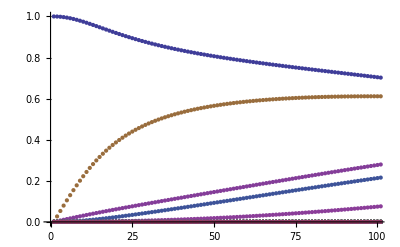

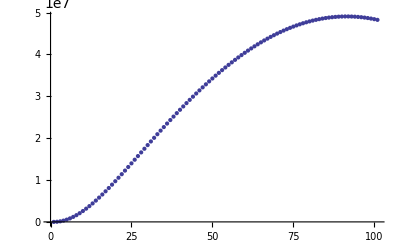

{5,0,1/2,1,-1}

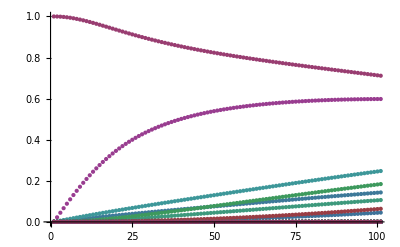

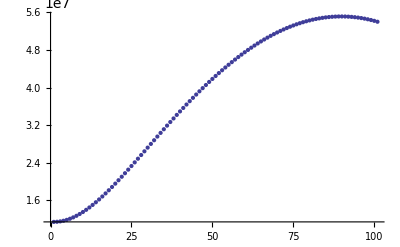

{5,0,1/2,1,0}

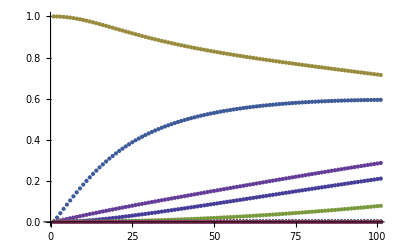

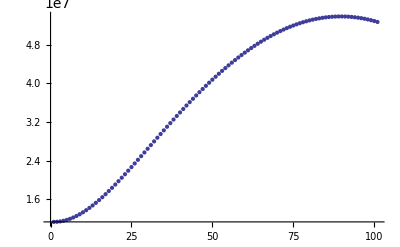

{5,0,1/2,1,1}

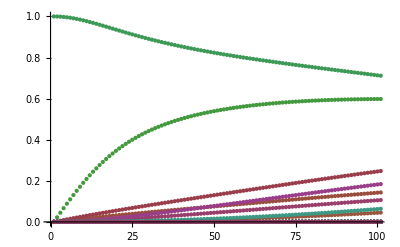

-Graphics-

{5,1,1/2,0,0}

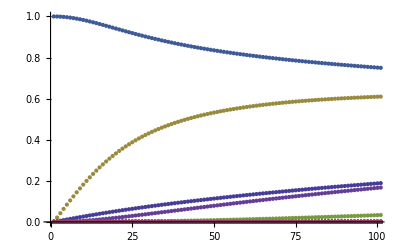

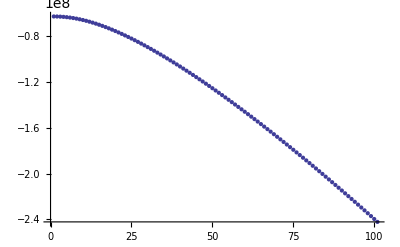

{5,1,1/2,1,-1}

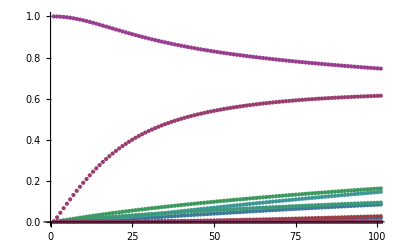

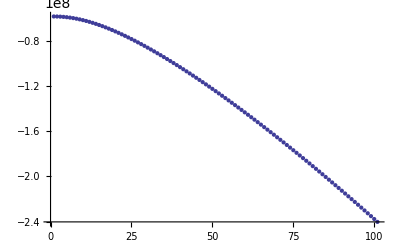

{5,1,1/2,1,0}

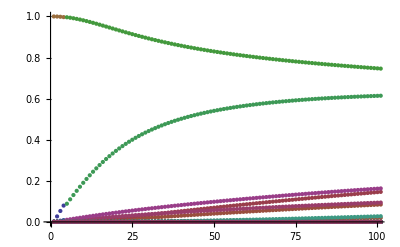

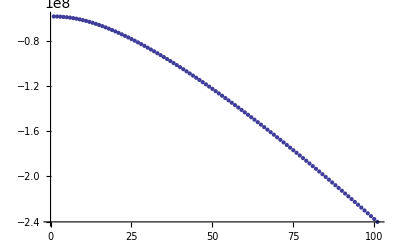

{5,1,1/2,1,1}

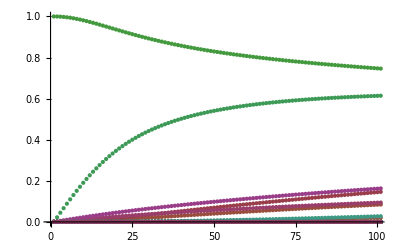

-Graphics-

{5,1,3/2,1,-1}

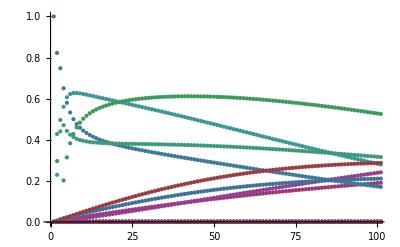

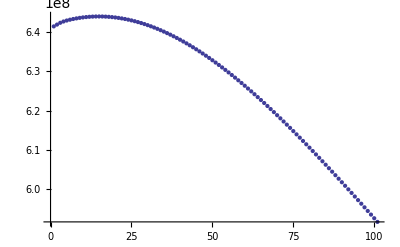

{5,1,3/2,1,0}

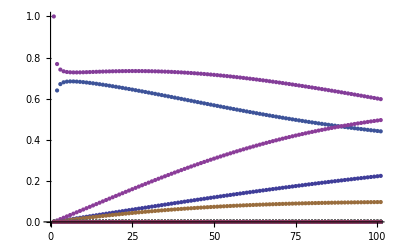

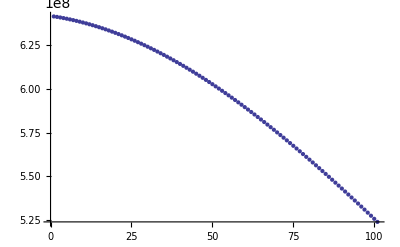

{5,1,3/2,1,1}

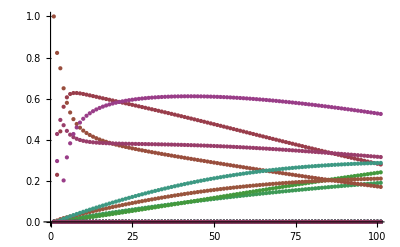

-Graphics-

{5,1,3/2,2,-2}

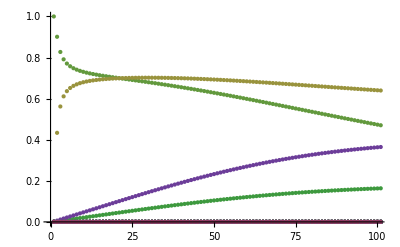

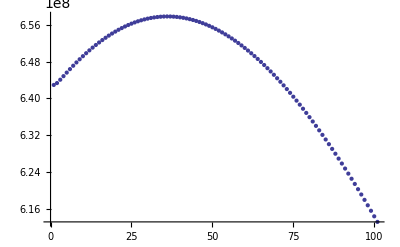

{5,1,3/2,2,-1}

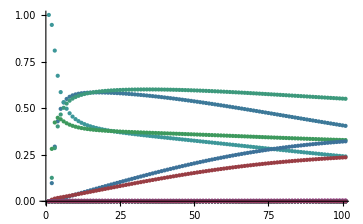

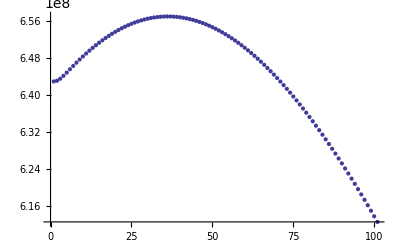

{5,1,3/2,2,0}

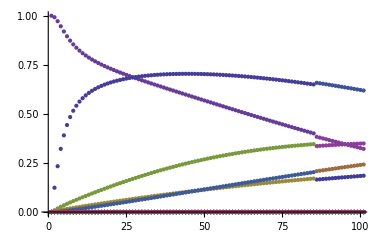

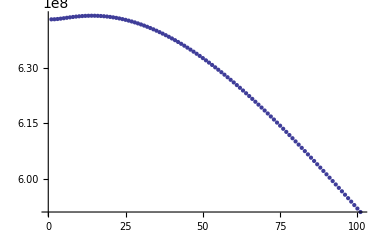

{5,1,3/2,2,1}

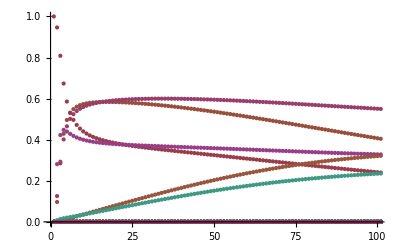

-Graphics-

{5,1,3/2,2,2}

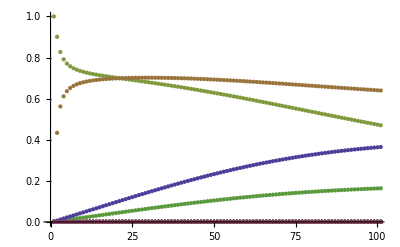

-Graphics-

{5,2,3/2,1,-1}

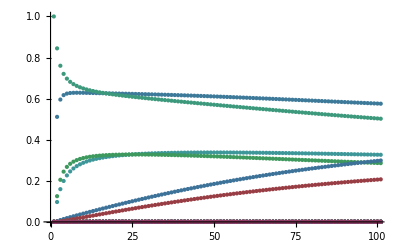

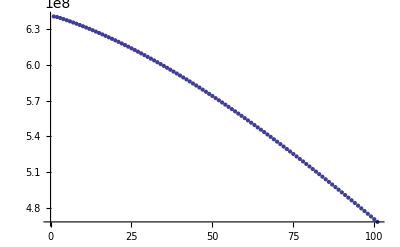

{5,2,3/2,1,0}

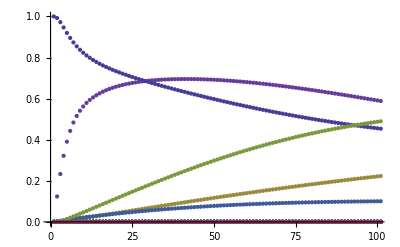

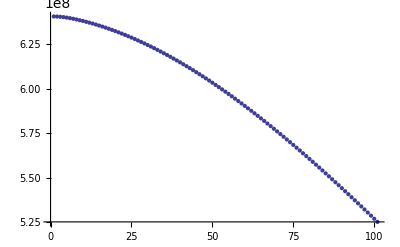

{5,2,3/2,1,1}

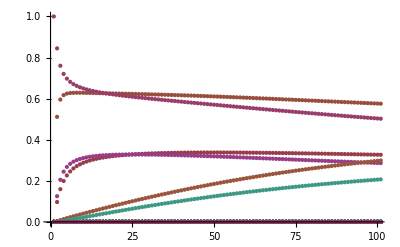

-Graphics-

{5,2,3/2,2,-2}

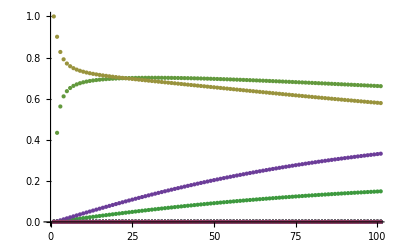

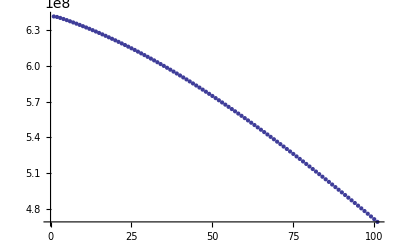

{5,2,3/2,2,-1}

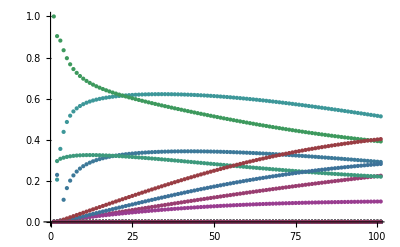

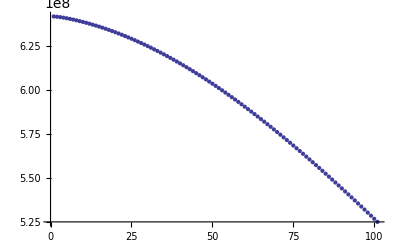

{5,2,3/2,2,0}

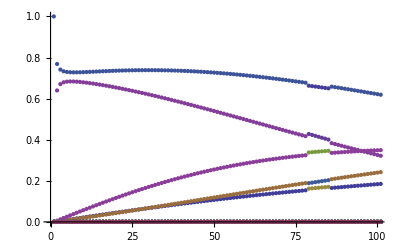

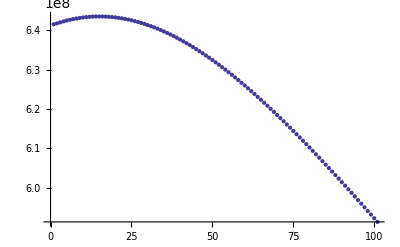

{5,2,3/2,2,1}

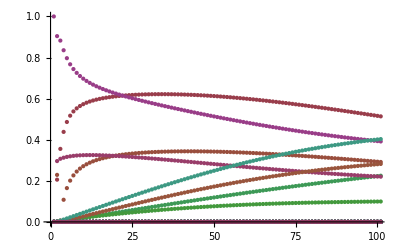

-Graphics-

{5,2,3/2,2,2}

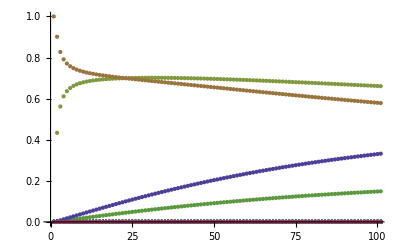

-Graphics-

{5,2,5/2,2,-2}

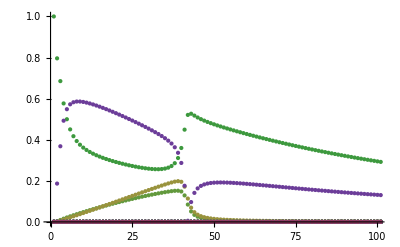

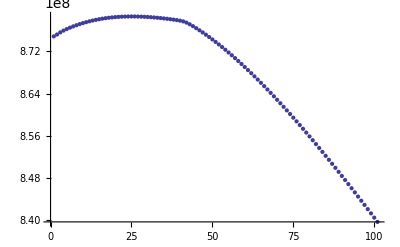

{5,2,5/2,2,-1}

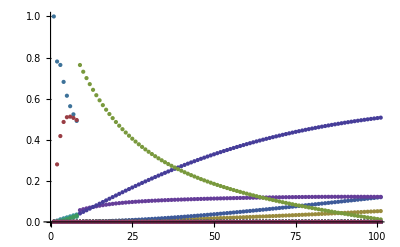

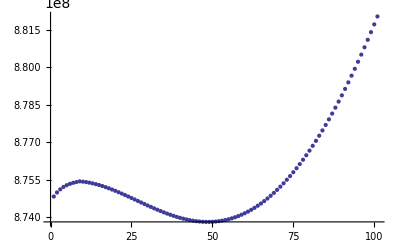

{5,2,5/2,2,0}

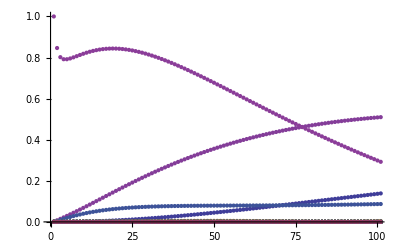

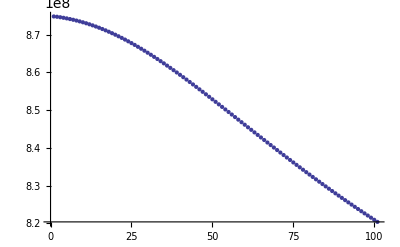

{5,2,5/2,2,1}

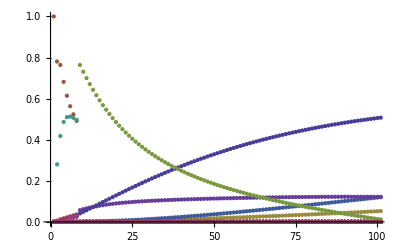

-Graphics-

{5,2,5/2,2,2}

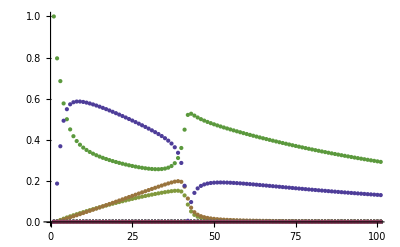

-Graphics-

{5,2,5/2,3,-3}

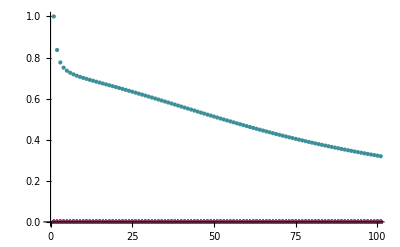

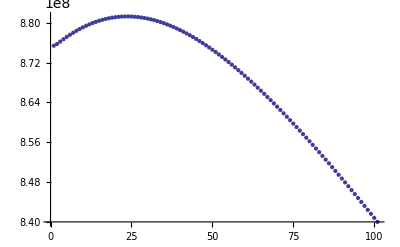

{5,2,5/2,3,-2}

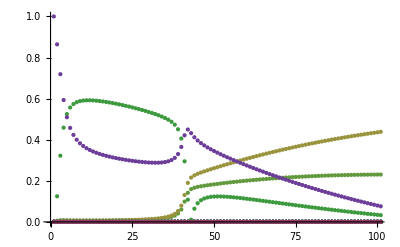

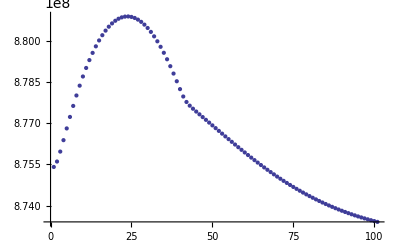

{5,2,5/2,3,-1}

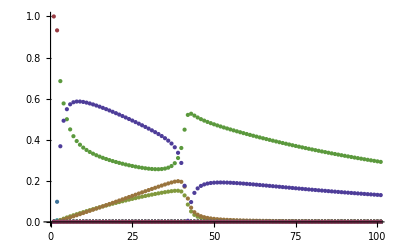

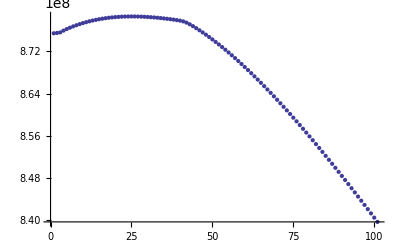

{5,2,5/2,3,0}

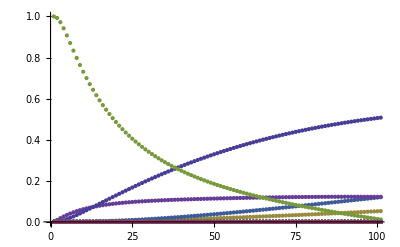

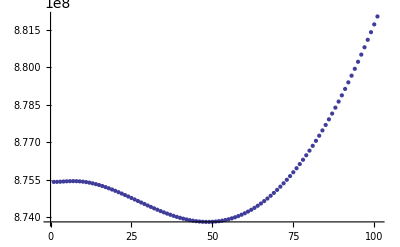

{5,2,5/2,3,1}

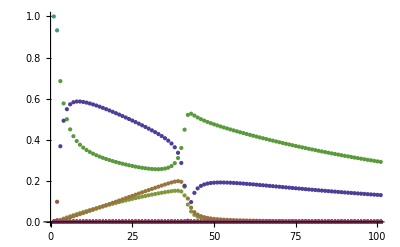

-Graphics-

{5,2,5/2,3,2}

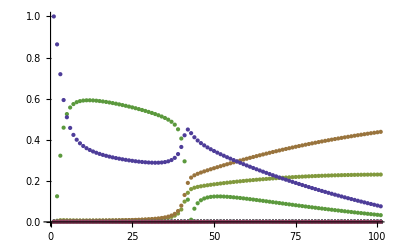

-Graphics-

{5,2,5/2,3,3}

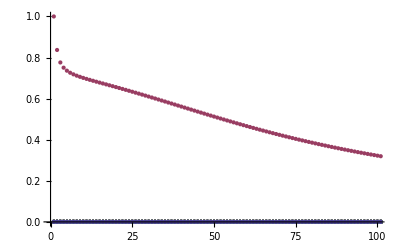

-Graphics-

{5,3,5/2,2,-2}

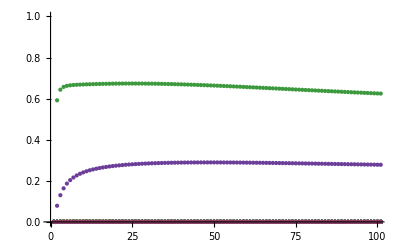

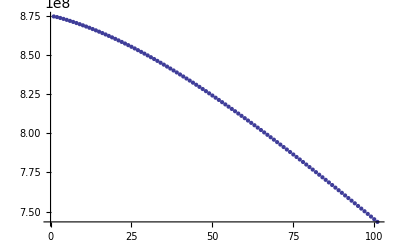

{5,3,5/2,2,-1}

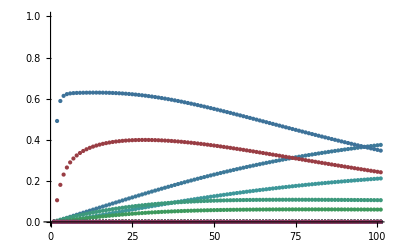

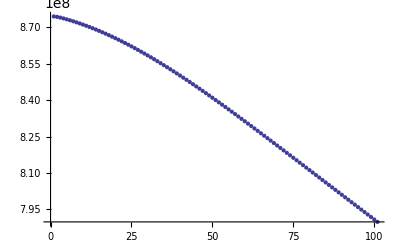

{5,3,5/2,2,0}

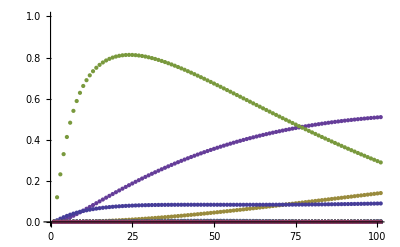

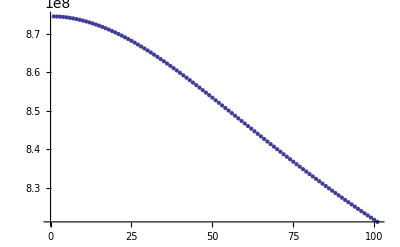

{5,3,5/2,2,1}

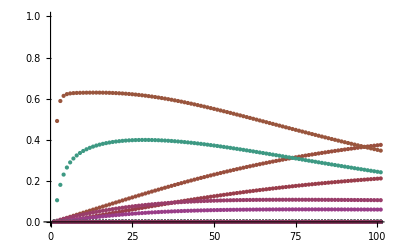

-Graphics-

{5,3,5/2,2,2}

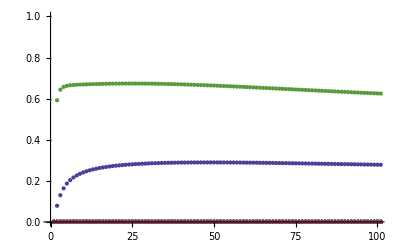

-Graphics-

{5,3,5/2,3,-3}

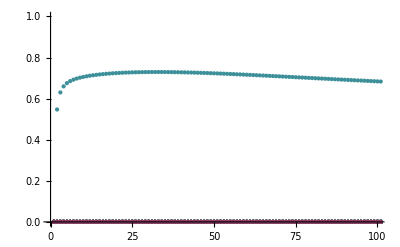

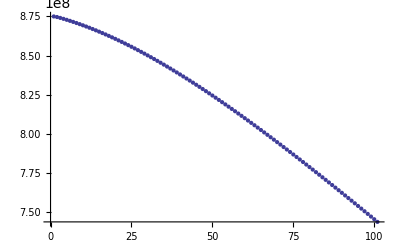

{5,3,5/2,3,-2}

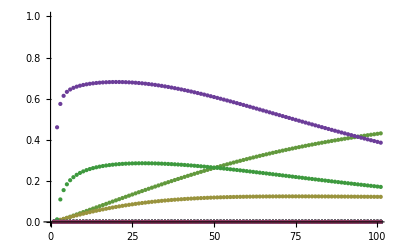

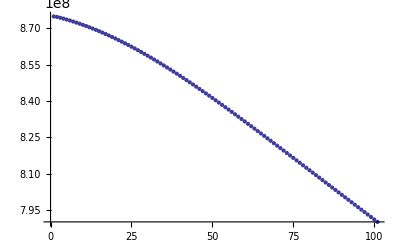

{5,3,5/2,3,-1}

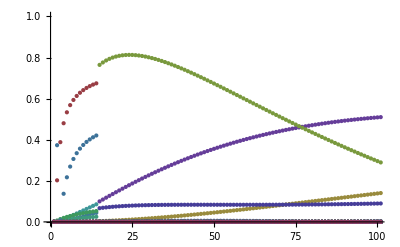

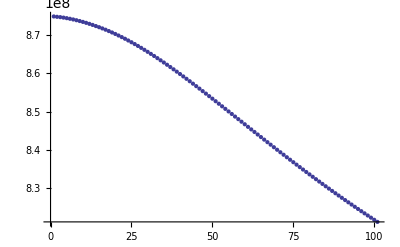

{5,3,5/2,3,0}

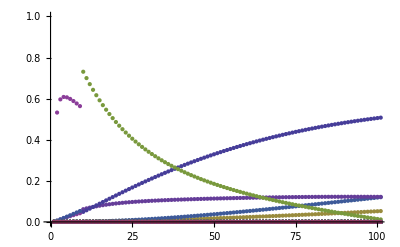

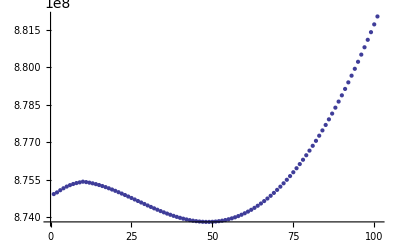

{5,3,5/2,3,1}

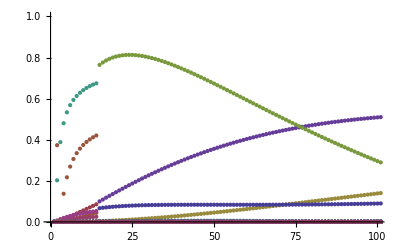

-Graphics-

{5,3,5/2,3,2}

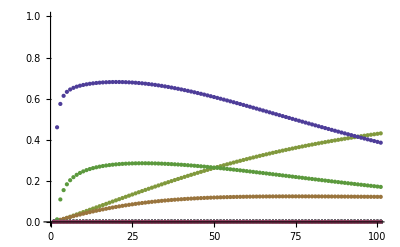

-Graphics-

{5,3,5/2,3,3}

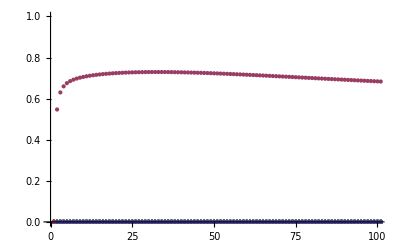

-Graphics-

{5,3,7/2,3,-3}

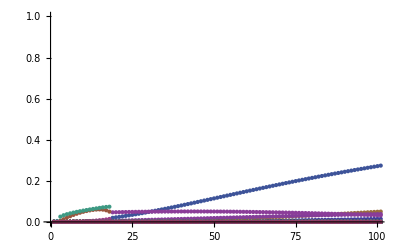

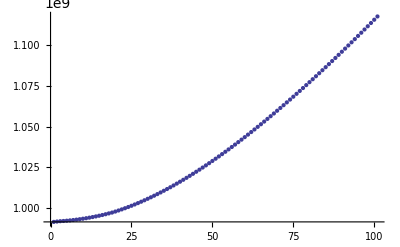

{5,3,7/2,3,-2}

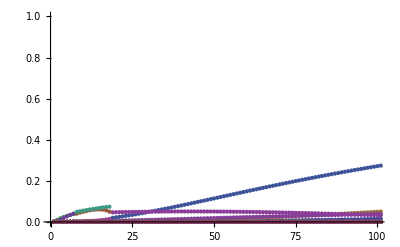

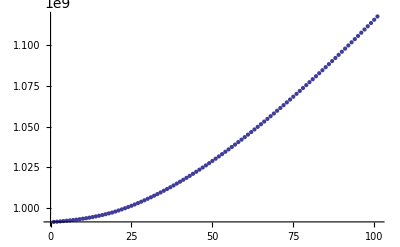

{5,3,7/2,3,-1}

Part::partd: Part specification {{{{1., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 50 »}, « 49 », « 50 »}, « 49 », « 51 »}, {{0, 11363600, 11363600, 11363600, -62512300, -58725400, -58725400, -58725400, 641399600, « 33 », 874921000, 874921000, 874921000, 874921000, 874921000, 874921000, 991573300, 991573300, « 50 »}, « 49 », « 51 »}} ⟦ 1, 1 ;; All, « 2 », 1 ⟧ is longer than depth of object.

Part::partd: Part specification {{{{1., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 50 »}, « 49 », « 50 »}, « 49 », « 51 »}, {{0, 11363600, 11363600, 11363600, -62512300, -58725400, -58725400, -58725400, 641399600, « 33 », 874921000, 874921000, 874921000, 874921000, 874921000, 874921000, 991573300, 991573300, « 50 »}, « 49 », « 51 »}} ⟦ 1, 1 ;; All, « 2 », 2 ⟧ is longer than depth of object.

Part::partd: Part specification {{{{1., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 50 »}, « 49 », « 50 »}, « 49 », « 51 »}, {{0, 11363600, 11363600, 11363600, -62512300, -58725400, -58725400, -58725400, 641399600, « 33 », 874921000, 874921000, 874921000, 874921000, 874921000, 874921000, 991573300, 991573300, « 50 »}, « 49 », « 51 »}} ⟦ 1, 1 ;; All, « 2 », 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

-Graphics-

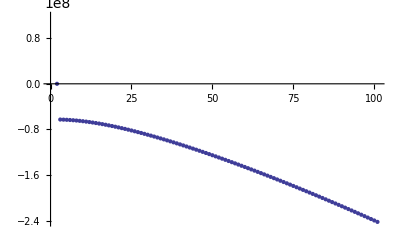

{5,3,7/2,3,0}

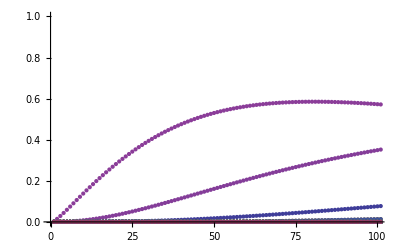

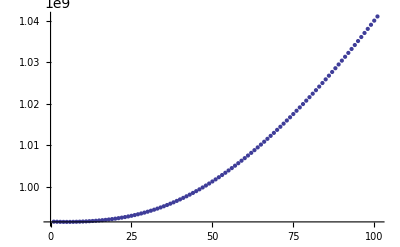

{5,3,7/2,3,1}

-Graphics-

-Graphics-

{5,3,7/2,3,2}

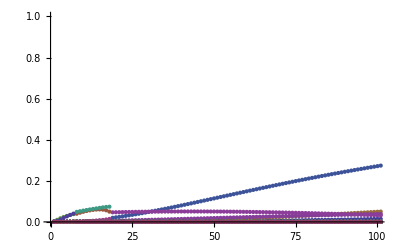

-Graphics-

{5,3,7/2,3,3}

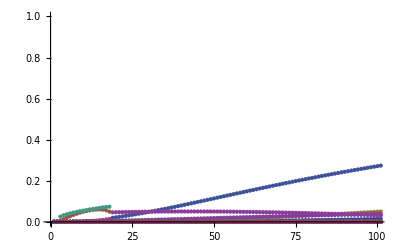

-Graphics-

{5,3,7/2,4,-4}

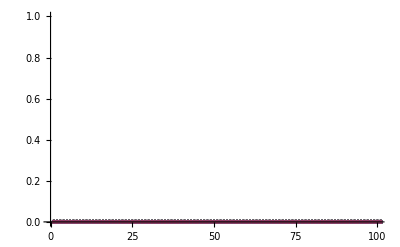

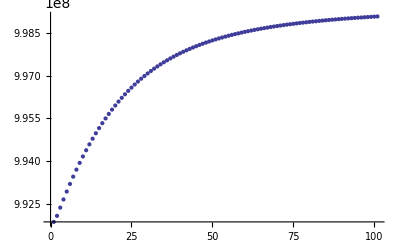

{5,3,7/2,4,-3}

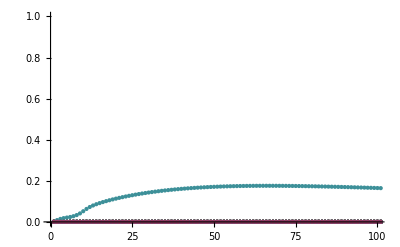

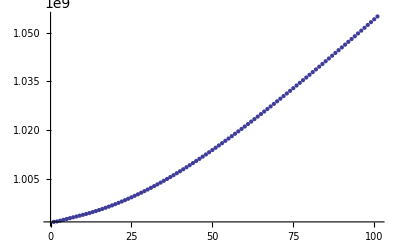

{5,3,7/2,4,-2}

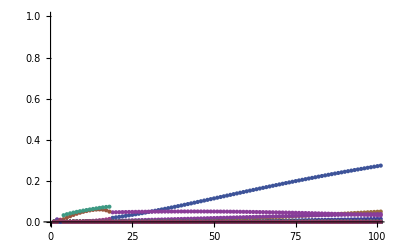

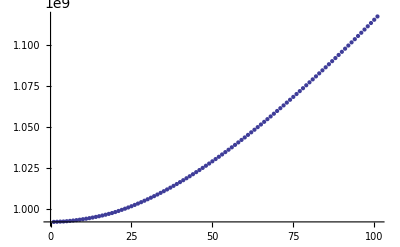

{5,3,7/2,4,-1}

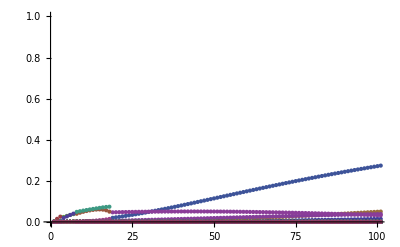

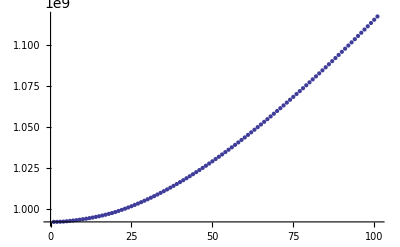

{5,3,7/2,4,0}

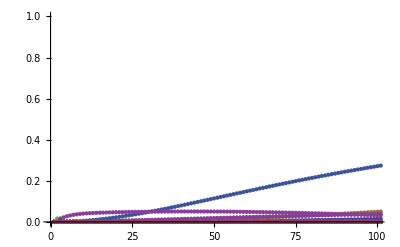

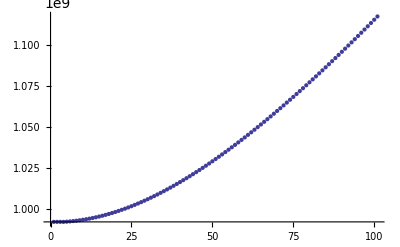

{5,3,7/2,4,1}

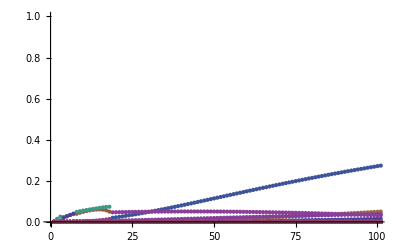

-Graphics-

{5,3,7/2,4,2}

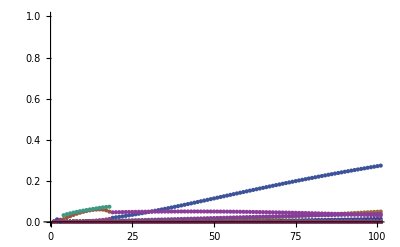

-Graphics-

{5,3,7/2,4,3}

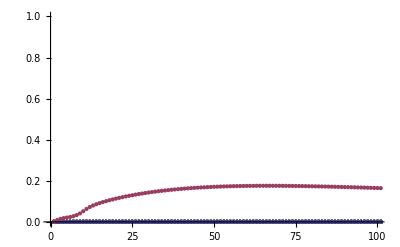

-Graphics-

{5,3,7/2,4,4}

-Graphics-

-Graphics-

{5,4,7/2,3,-3}

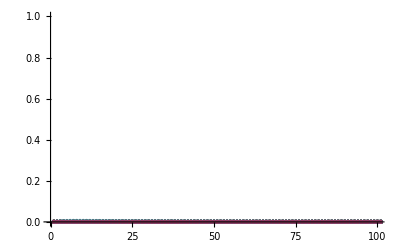

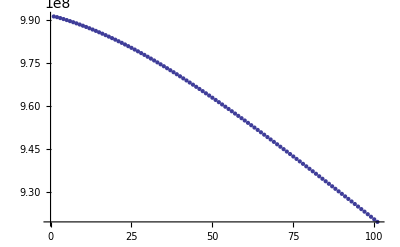

{5,4,7/2,3,-2}

-Graphics-

-Graphics-

{5,4,7/2,3,-1}

-Graphics-

-Graphics-

{5,4,7/2,3,0}

-Graphics-

-Graphics-

{5,4,7/2,3,1}

-Graphics-

-Graphics-

{5,4,7/2,3,2}

-Graphics-

-Graphics-

{5,4,7/2,3,3}

-Graphics-

-Graphics-

{5,4,7/2,4,-4}

-Graphics-

-Graphics-

{5,4,7/2,4,-3}

-Graphics-

-Graphics-

{5,4,7/2,4,-2}

-Graphics-

-Graphics-

{5,4,7/2,4,-1}

-Graphics-

-Graphics-

{5,4,7/2,4,0}

-Graphics-

-Graphics-

{5,4,7/2,4,1}

-Graphics-

-Graphics-

{5,4,7/2,4,2}

-Graphics-

-Graphics-

{5,4,7/2,4,3}

-Graphics-

-Graphics-

{5,4,7/2,4,4}

-Graphics-

-Graphics-

{5,4,9/2,4,-4}

-Graphics-

-Graphics-

{5,4,9/2,4,-3}

-Graphics-

-Graphics-

{5,4,9/2,4,-2}

-Graphics-

-Graphics-

{5,4,9/2,4,-1}

-Graphics-

-Graphics-

{5,4,9/2,4,0}

-Graphics-

-Graphics-

{5,4,9/2,4,1}

-Graphics-

-Graphics-

{5,4,9/2,4,2}

-Graphics-

-Graphics-

{5,4,9/2,4,3}

-Graphics-

-Graphics-

{5,4,9/2,4,4}

-Graphics-

-Graphics-

{5,4,9/2,5,-5}

-Graphics-

-Graphics-

{5,4,9/2,5,-4}

-Graphics-

-Graphics-

{5,4,9/2,5,-3}

-Graphics-

-Graphics-

{5,4,9/2,5,-2}

-Graphics-

-Graphics-

{5,4,9/2,5,-1}

-Graphics-

-Graphics-

{5,4,9/2,5,0}

-Graphics-

-Graphics-

{5,4,9/2,5,1}

-Graphics-

-Graphics-

{5,4,9/2,5,2}

-Graphics-

-Graphics-

{5,4,9/2,5,3}

-Graphics-

-Graphics-

{5,4,9/2,5,4}

-Graphics-

-Graphics-

{5,4,9/2,5,5}

-Graphics-

-Graphics-

0 1/2 0

-Graphics-

0 1/2 1

-Graphics-

1 1/2 0

-Graphics-

1 1/2 1

-Graphics-

1 3/2 1

-Graphics-

1 3/2 2

-Graphics-

2 3/2 1

-Graphics-

2 3/2 2

-Graphics-

2 5/2 2

-Graphics-

2 5/2 3

-Graphics-

3 5/2 2

-Graphics-

3 5/2 3

-Graphics-

3 7/2 3

-Graphics-

3 7/2 4

-Graphics-

4 7/2 3

-Graphics-

4 7/2 4

-Graphics-

4 9/2 4

-Graphics-

4 9/2 5

-Graphics-

```mathematica
Do[
Print[lst⟦k⟧];
Print@ListPlot[Table[Abs@sseg⟦1,;;,k,j⟧,{j,36}],PlotRange->{{0,100},{0,1}}];
Print@ListPlot[sseg⟦2,;;,k⟧];
,{k,Length[sseg⟦2,1⟧]}]
Do[
Do[
Do[
listofens={};
Do[
listofens=If[lst⟦state,2;;4⟧=={l,j,f},Join[listofens,{sseg⟦2,;;,state⟧}],listofens]
,{state,Length[lst]}]
If[Length[listofens]>0,
Print[l,j,f]
Print@ListPlot[listofens]];
,{f,Min[lst⟦;;,4⟧],Max[lst⟦;;,4⟧]}]
,{j,Min[lst⟦;;,3⟧],Max[lst⟦;;,3⟧]}]
,{l,Min[lst⟦;;,2⟧],Max[lst⟦;;,2⟧]}]
```

```mathematica
{sortedevecs,sortedevals}=sortedstarkeigens[0.0,1.0,0.1,"z"];
sortedevals//MatrixForm
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification {{}} ⟦ 1, 1 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

General::stop: Further output of Part :: pspec will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

(«1»)

```mathematica
min=0.0;max=10.0,step=0.1;
allthevecs=Table[starkeigen[efield,"z",If[efield==min+step,True,False]]⟦1⟧,{efield,min,max,step}];
allthevals=Table[starkeigen[efield,"z",If[efield==min+step,True,False]]⟦2⟧,{efield,min,max,step}];
```

```mathematica
ListPlot[Table[Abs@allthevecs⟦;;,j,9⟧,{j,36}],PlotRange->{{0,1000},{0,1}}]
```

```mathematica
(*Plotting lifetime and atoms remaining after 1m vs electric field*)
ListPlot[Table[Exp[-300*10^-9/(1/Abs@Im@valsvecs[Efield]⟦1,2⟧)],{Efield,0.,60.}]]
ListPlot[Table[Abs@valsvecs[Efield]⟦2,2,Position[Abs@valsvecs[Efield]⟦2,2⟧,Max@Abs@valsvecs[Efield]⟦2,2⟧]⟦1,1⟧⟧,{Efield,0.,60.}]]
ListPlot[Table[1/Abs@Im@valsvecs[Efield]⟦1,-1⟧,{Efield,29.,31.}]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
n3zvecs32=Table[valsvecs[SetPrecision[ef,32]]⟦2⟧,{ef,0.,10.0,0.1}];
n3zvals32=Table[valsvecs[SetPrecision[ef,32]]⟦1⟧,{ef,0.,10.0,0.1}];
n3zvecs32sorted=ConstantArray[0,{Length[n3zvecs32],Length[n3zvecs32⟦1⟧]}];
n3zvals32sorted=ConstantArray[0,{Length[n3zvecs32],Length[n3zvecs32⟦1⟧]}];
Do[Do[pos=Position[Abs[n3zvecs32⟦j,k⟧],Max[Abs[n3zvecs32⟦j,k⟧]]]⟦1,1⟧;
n3zvecs32sorted⟦j,pos⟧=n3zvecs32⟦j,k⟧;
n3zvals32sorted⟦j,pos⟧=n3zvals32⟦j,k⟧;
,{k,Length[n3zvecs32⟦j⟧]}],{j,Length[n3zvecs32]}];
Print["Done 32 bit precision."]
```

$Aborted

$Aborted

Part::partd: Part specification n3zvecs32 ⟦ 1 ⟧ is longer than depth of object.

Done 32 bit precision.

```mathematica
n3zvecsmc=Table[valsvecs[ef]⟦2⟧,{ef,0,10,0.01}];
n3zvalsmc=Table[valsvecs[ef]⟦1⟧,{ef,0,10,0.01}];
n3zvecsmcsorted=ConstantArray[0,{Length[n3zvecsmc],Length[n3zvecsmc⟦1⟧]}];
n3zvalsmcsorted=ConstantArray[0,{Length[n3zvecsmc],Length[n3zvecsmc⟦1⟧]}];
Do[Do[pos=Position[Abs[n3zvecsmc⟦j,k⟧],Max[Abs[n3zvecsmc⟦j,k⟧]]]⟦1,1⟧;
n3zvecsmcsorted⟦j,pos⟧=n3zvecsmc⟦j,k⟧;
n3zvalsmcsorted⟦j,pos⟧=n3zvalsmc⟦j,k⟧;
,{k,Length[n3zvecsmc⟦j⟧]}],{j,Length[n3zvecsmc]}];
Print["Done machine precision."]
```

Done machine precision.

```mathematica
n3zvalsasol=Eigenvalues[newmtx[Efield]];
```

```mathematica
somevec={a,b,c,d,e,f,g,h,j,k,l,n,o,p,q,r,t,u,v,w,x,y,z,A,B,F,G,H,J,L,M,Q,R,S,T,U};
Solve[newmtx[Efield].{a,b,c,d,e,f,g,h,j,k,l,n,o,p,q,r,t,u,v,w,x,y,z,A,B,F,G,H,J,L,M,Q,R,S,T,U}==n3zvalsasol⟦4⟧*{a,b,c,d,e,f,g,h,j,k,l,n,o,p,q,r,t,u,v,w,x,y,z,A,B,F,G,H,J,L,M,Q,R,S,T,U},a]
```

$Aborted

```mathematica
n3zvecsasorted=ConstantArray[0,{Length[n3zvecsa],Length[n3zvecsa⟦1⟧]}];
n3zvalsasorted=ConstantArray[0,{Length[n3zvecsa],Length[n3zvecsa⟦1⟧]}];
Do[Do[pos=Position[Abs[n3zvecsa⟦j,k⟧],Max[Abs[n3zvecsa⟦j,k⟧]]]⟦1,1⟧;
n3zvecsasorted⟦j,pos⟧=n3zvecsa⟦j,k⟧;
n3zvalsasorted⟦j,pos⟧=n3zvalsa⟦j,k⟧;
,{k,Length[n3zvecsa⟦j⟧]}],{j,Length[n3zvecsa]}];
Print["Done analytic."]
```

Done 32 bit precision.

Done machine precision.

$Aborted

Part::partd: Part specification n3zvalsa ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification n3zvalsa ⟦ 1, 2 ⟧ is longer than depth of object.

Part::partd: Part specification n3zvalsa ⟦ 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

$Aborted

Done analytic.

```mathematica
n3zvecs32r=Table[valsvecs[SetPrecision[ef,32]]⟦2⟧,{ef,0.,10.0,0.1}];
n3zvals32r=Table[valsvecs[SetPrecision[ef,32]]⟦1⟧,{ef,0.,10.0,0.1}];
n3zvecs32rsorted=ConstantArray[0,{Length[n3zvecs32r],Length[n3zvecs32r⟦1⟧]}];
n3zvals32rsorted=ConstantArray[0,{Length[n3zvals32r],Length[n3zvals32r⟦1⟧]}];
Do[Do[pos=Position[Abs[n3zvecs32r⟦j,k⟧],Max[Abs[n3zvecs32r⟦j,k⟧]]]⟦1,1⟧;
n3zvecs32rsorted⟦j,pos⟧=n3zvecs32r⟦j,k⟧;
n3zvals32rsorted⟦j,pos⟧=n3zvals32r⟦j,k⟧;
,{k,Length[n3zvecs32r⟦j⟧]}],{j,Length[n3zvecs32r]}];
Print["Done 32 bit precision."]
```

Done 32 bit precision.

```mathematica
n3zvecsrmc=Table[valsvecs[ef]⟦2⟧,{ef,0,10,0.1}];
n3zvalsrmc=Table[valsvecs[ef]⟦1⟧,{ef,0,10,0.1}];
n3zvecsrmcsorted=ConstantArray[0,{Length[n3zvecsrmc],Length[n3zvecsrmc⟦1⟧]}];
n3zvalsrmcsorted=ConstantArray[0,{Length[n3zvecsrmc],Length[n3zvecsrmc⟦1⟧]}];
Do[Do[pos=Position[Abs[n3zvecsrmc⟦j,k⟧],Max[Abs[n3zvecsrmc⟦j,k⟧]]]⟦1,1⟧;
n3zvecsrmcsorted⟦j,pos⟧=n3zvecsrmc⟦j,k⟧;
n3zvalsrmcsorted⟦j,pos⟧=n3zvalsrmc⟦j,k⟧;
,{k,Length[n3zvecsrmc⟦j⟧]}],{j,Length[n3zvecsrmc]}];
Print["Done machine precision."]
```

Done machine precision.

```mathematica
lst⟦16⟧
somevec={a,b,c,d,e,f,g,h,j,k,l,n,o,p,q,r,t,u,v,w,x,y,z,A,B,F,G,H,J,L,M,Q,R,S,T,U};
Solve[(newmtx[SetPrecision[10.0,50]]-Eigenvalues[newmtx[SetPrecision[10.0,50]]]⟦4⟧*IdentityMatrix[36]).somevec==ConstantArray[0,36],somevec]
(newmtx[10.0]-Eigenvalues[newmtx[10.0]]⟦1⟧*IdentityMatrix[36]).somevec//MatrixForm;
```

{3,1,3/2,2,2}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→0,b→0,c→0,d→0,e→0,f→0,g→0,h→0,j→0,k→0,l→0,o→0,p→0,q→0,t→0,u→0,v→0,w→-0.023743236958640334328412243029078354381207242 n,x→0,y→0,z→0,A→0.023743236958640334328412243029078354381207242 r,B→-4.2569905571218747138316546340064549065457838 n,F→0,G→0,H→0,J→4.2569905571218747138316546340064549065457838 r,L→0,M→-21.016097616098432722125307595135738670733528 n,Q→0,R→0,S→0,T→-21.016097616098432722125307595135738670733528 r,U→0}}

```mathematica
thisj=32;
lst⟦thisj⟧;
Abs@n3zvecsmcsorted⟦;;,32⟧//MatrixForm;
ListPlot[Table[Abs@n3zvecsmc⟦;;,2,j⟧,{j,36}],PlotRange->{{0,1001},{0,1}}]
ListPlot[Table[Abs@n3zvalsmc⟦;;,x⟧,{x,36}]]
```

-Graphics-

-Graphics-

```mathematica
n2zvecs=Table[valsvecs[SetPrecision[Rationalize[ef],32]]⟦2⟧,{ef,0,2,0.1}];
n2zvecs=Table[Table[Normalize[n2zvecs⟦j,k⟧],{k,Length[n2zvecs⟦j⟧]}],{j,Length[n2zvecs]}];
(*n2zvals=Table[valsvecs[Rationalize[ef]]⟦1⟧,{ef,0,2,0.1}];*)
n2zvecssorted=ConstantArray[0,{Length[n2zvecs],totalstates[3]}];
(*n2zvalssorted=ConstantArray[0,{Length[n2zvals],totalstates[3]}];*)
Do[Do[pos=Position[Abs[n2zvecs⟦j,k⟧],Max[Abs[n2zvecs⟦j,k⟧]]]⟦1,1⟧;
n2zvecssorted⟦j,pos⟧=n2zvecs⟦j,k⟧;
(*n2zvalssorted⟦j,pos⟧=n2zvals⟦j,k⟧;*),{k,Length[n2zvecs⟦j⟧]}],{j,Length[n2zvecs]}];
```

```mathematica
st=16;
n2zvecssorted⟦;;,st,Position[Abs[n2zvecssorted⟦1,st⟧],Max[Abs[n2zvecssorted⟦1,st⟧]]]⟦1,1⟧⟧//MatrixForm;
ListPlot[Abs[n2zvecssorted⟦;;,st,Position[Abs[n2zvecssorted⟦1,st⟧],Max[Abs[n2zvecssorted⟦1,st⟧]]]⟦1,1⟧⟧]]
n2zvecs⟦1,1⟧//MatrixForm;
n2zvecs⟦2⟧//MatrixForm;
```

-Graphics-

-Graphics-

```mathematica
190
```

-Graphics-

```mathematica
150
```

-Graphics-

```mathematica
200
```

-Graphics-

-Graphics-

```mathematica
50
```

-Graphics-

```mathematica
40
```

-Graphics-

```mathematica
30
```

-Graphics-

```mathematica
20
```

-Graphics-

```mathematica
10
```

-Graphics-

```mathematica
(* Saving an analytic solution to the eigenvalue problem for the specified matrix. *)
(* Make sure to change the name of the variables, the file, AND the variables being saved. *)
(* Clear[Efield]; *)
Timing[Do[
{n2yvals,n2yvecs}=valsvecs[efield];
fstr=ToString[efield];
Export["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n2ystark"<>fstr<>"evals.dat",n2yvals];
Export["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n2ystark"<>fstr<>"evecs.dat",n2yvecs];,{efield,0,60,0.5}]]
```

{1.88761,Null}

```mathematica
Clear[n1xvals,n1yvals,n1zvals,n2xvals,n2yvals,n2zvals,n3xvals,n3yvals,n3zvals,n1xvecs,n1yvecs,n1zvecs,n2xvecs,n2yvecs,n2zvecs,n3xvecs,n3yvecs,n3zvecs];
```

```mathematica
(* Mapping out the stark fan for n=2 *)
n2zvals=ConstantArray[0,121];
n2zvecs=ConstantArray[0,121];
Do[
fstr=ToString[0.5*j];
n2zvals⟦j+1⟧=ToExpression[Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n2zstark"<>fstr<>"evals.dat","Table"]];
n2zvecs⟦j+1⟧=ToExpression[Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n2zstark"<>fstr<>"evecs.dat","Table"]];
,{j,0,120}]
```

```mathematica
lst;
Table[Max@Abs@n2zvecs⟦j,12⟧,{j,121}]//MatrixForm;
ListPlot[Table[Flatten@Re@n2zvals⟦;;,j⟧,{j,13,14}]]
```

-Graphics-

```mathematica
(* In order for the dipole matrix elements to be calculated properly, you need to add zeros on *)
(* to the end and beginning of the current eigenvectors. These functions accomplish that. *)
makebigvec[evec_,n_,nmax_]:=Join[ConstantArray[0.,Sum[totalstates[j],{j,0,n-1}]],evec,ConstantArray[0.,Sum[totalstates[j],{j,0,nmax}]-Sum[totalstates[j],{j,0,n}]]]
makebigveclist[eveclist_,n_,nmax_]:=(newlist=ConstantArray[0.,{Length[eveclist],Length[eveclist[[1]]]}];Do[newlist[[j]]=makebigvec[eveclist[[j]],n,nmax],{j,Length[eveclist]}];newlist)
```

```mathematica
(* Imports the x, y, and z matrices for all states up to specified n. This is for use when *)(* calculating Stark state matrix elements. *)
nmax=3;
efield=30.0;
fielddirection="z";
strnmax=ToString[nmax];
strefield=ToString[efield];
biglist=Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n1to"<>strnmax<>"list.dat","Table"];
biglist=ToExpression[biglist];
bigxmatrix=Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n1to"<>strnmax<>"xmtrx.dat","Table"];
bigxmatrix=ToExpression[bigxmatrix];
bigymatrix=Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n1to"<>strnmax<>"ymtrx.dat","Table"];
bigymatrix=ToExpression[bigymatrix];
bigzmatrix=Import["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n1to"<>strnmax<>"zmtrx.dat","Table"];
bigzmatrix=ToExpression[bigzmatrix];
bigdmatrix=Table[{bigxmatrix⟦j,k⟧,bigymatrix⟦j,k⟧,bigzmatrix⟦j,k⟧},{j,Length[bigxmatrix]},{k,Length[bigxmatrix]}];
(* Make sure biglist matches the nmax here. *)
DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n1"<>fielddirection<>"starkevals.mx"];
DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n1"<>fielddirection<>"stark.mx"];
Do[DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n"<>ToString[n]<>fielddirection<>"stark"<>strefield<>"evals.mx"];
DumpGet["C:\\Users\\travis\\Google Drive\\Travis Code\\Simulations\\DCStark\\n"<>ToString[n]<>fielddirection<>"stark"<>strefield<>"evecs.mx"];
,{n,2,nmax}]
```

```mathematica
(* Unfortunately this must be tweaked manually for now *)
allvecs={n1zvecs,n2zvecs,n3zvecs};
allvals={n1zvals,n2zvals,n3zvals};
```

```mathematica
starks=ConstantArray[0,Length[biglist]];
starksens=ConstantArray[0,Length[biglist]];
starksgams=ConstantArray[0,Length[biglist]];
(* Append the elongated eigenvectors together to form a larger list of eigenvectors. *)
nvecs=Join[Flatten[allvecs,1]];
Do[Do[nvecs⟦Sum[totalstates[k],{k,0,n-1}]+j⟧=makebigvec[nvecs⟦Sum[totalstates[k],{k,0,n-1}]+j⟧,n,nmax],{j,1,totalstates[n]}],{n,1,nmax}];
nvecs//MatrixForm;
nvals=Join[Flatten[allvals,1]];
(* Also calculate the Stark energies and lifetimes (based on the imaginary part of the *)
(* calculated eigenvalues. *)
Do[starksens[[j]]=Re[nvals[[j]]],{j,Length[nvals]}]
Do[starksgams[[j]]=Im[nvals[[j]]],{j,Length[nvals]}]
Do[starks[[j]]=Normalize[nvecs[[j]]],{j,Length[nvecs]}]
Do[thisstark={};Do[If[Abs[N[starks[[j,k]],10]]>0,thisstark=Append[thisstark,Append[{k,N[starks[[j,k]],10]},biglist[[k]]]],None],{k,Length[starks[[j]]]}];starks[[j]]=thisstark,{j,Length[starks]}]
starks//MatrixForm
```

```mathematica
(* Functions to calculate the dipole matrix elements for the Stark states. *)
stufftoadd={r,θ,ϕ,1};
starkxEV[stark1_,stark2_]:=(sum=0.0;Do[p1=stark1[[j,1]];p2=stark2[[k,1]];sum=sum+Conjugate[stark1[[j,2]]]*stark2[[k,2]]*bigxmatrix[[p1,p2]],{j,Length[stark1]},{k,Length[stark2]}];sum)
starkyEV[stark1_,stark2_]:=(sum=0.0;Do[p1=stark1[[j,1]];p2=stark2[[k,1]];sum=sum+Conjugate[stark1[[j,2]]]*stark2[[k,2]]*bigymatrix[[p1,p2]],{j,Length[stark1]},{k,Length[stark2]}];sum)
starkzEV[stark1_,stark2_]:=(sum=0.0;Do[p1=stark1[[j,1]];p2=stark2[[k,1]];sum=sum+Conjugate[stark1[[j,2]]]*stark2[[k,2]]*bigzmatrix[[p1,p2]],{j,Length[stark1]},{k,Length[stark2]}];sum)
```

```mathematica
(* Calculating the elements of the dipole matrices. *)
Timing[starkxmatrix=Table[Table[starkxEV[starks[[j]],starks[[k]]],{j,Length[starks]}],{k,Length[starks]}];]
starkxmatrix//MatrixForm
starkymatrix=Table[Table[starkyEV[starks[[j]],starks[[k]]],{j,Length[starks]}],{k,Length[starks]}];
starkymatrix//MatrixForm
starkzmatrix=Table[Table[starkzEV[starks[[j]],starks[[k]]],{j,Length[starks]}],{k,Length[starks]}];
starkzmatrix//MatrixForm
starkdmatrix=Table[{starkxmatrix⟦j,k⟧,starkymatrix⟦j,k⟧,starkzmatrix⟦j,k⟧},{j,Length[starkxmatrix]},{k,Length[starkxmatrix]}];
starkdmatrix//MatrixForm
```

{14.18049,Null}

(«1»)

(«1»)

(«1»)

«1 more identical outputs»

```mathematica
biglist
```

{{1,0,1/2,0,0},{1,0,1/2,1,-1},{1,0,1/2,1,0},{1,0,1/2,1,1},{2,0,1/2,0,0},{2,0,1/2,1,-1},{2,0,1/2,1,0},{2,0,1/2,1,1},{2,1,1/2,0,0},{2,1,1/2,1,-1},{2,1,1/2,1,0},{2,1,1/2,1,1},{2,1,3/2,1,-1},{2,1,3/2,1,0},{2,1,3/2,1,1},{2,1,3/2,2,-2},{2,1,3/2,2,-1},{2,1,3/2,2,0},{2,1,3/2,2,1},{2,1,3/2,2,2},{3,0,1/2,0,0},{3,0,1/2,1,-1},{3,0,1/2,1,0},{3,0,1/2,1,1},{3,1,1/2,0,0},{3,1,1/2,1,-1},{3,1,1/2,1,0},{3,1,1/2,1,1},{3,1,3/2,1,-1},{3,1,3/2,1,0},{3,1,3/2,1,1},{3,1,3/2,2,-2},{3,1,3/2,2,-1},{3,1,3/2,2,0},{3,1,3/2,2,1},{3,1,3/2,2,2},{3,2,3/2,1,-1},{3,2,3/2,1,0},{3,2,3/2,1,1},{3,2,3/2,2,-2},{3,2,3/2,2,-1},{3,2,3/2,2,0},{3,2,3/2,2,1},{3,2,3/2,2,2},{3,2,5/2,2,-2},{3,2,5/2,2,-1},{3,2,5/2,2,0},{3,2,5/2,2,1},{3,2,5/2,2,2},{3,2,5/2,3,-3},{3,2,5/2,3,-2},{3,2,5/2,3,-1},{3,2,5/2,3,0},{3,2,5/2,3,1},{3,2,5/2,3,2},{3,2,5/2,3,3}}

```mathematica
(* Functions to calculate the lifetimes of the non-Stark HFS states. *)
(* In order to calculate the lifetime of a particular |n,l,j,f,m_f> state, you need to know its index *)
(* in the biglist. *)
totenergies=ConstantArray[0,Length[biglist]];
nmax=2;
hfsenergies=Flatten[Table[Table[Table[Table[Table[energytable[[n,l+1,j+1/2-l+1,f+1/2-j+1]],{mf,-f,f}],{f,j-1/2,j+1/2}],{j,Max[l-1/2,1/2],l+1/2}],{l,0,n-1}],{n,1,nmax}]];
Do[totenergies[[Sum[totalstates[k],{k,0,j-1}]+1;;Sum[totalstates[k],{k,0,j}]]]=N[-1/j^2,10],{j,1,nmax}]
Do[totenergies[[j]]=totenergies[[j]]+hfsenergies[[j]]/(RyCODATA*cCODATA),{j,Length[hfsenergies]}]
N[totenergies,20]//MatrixForm;
hfslt[hfsnum_]:=const*eCODATA^2/Sum[If[totenergies[[hfsnum]]>totenergies[[j]],(Abs[totenergies[[hfsnum]]-totenergies[[j]]])^3,0]*(2*π*hbarCODATA)^2*Dot[{bigxmatrix[[hfsnum,j]],bigymatrix[[hfsnum,j]],bigzmatrix[[hfsnum,j]]},Conjugate[{bigxmatrix[[hfsnum,j]],bigymatrix[[hfsnum,j]],bigzmatrix[[hfsnum,j]]}]]/aμ^2,{j,1,Length[bigzmatrix]}]
hfslt[20]
```

1.59998321

```mathematica
(* Calculating Stark state lifetimes using the dipole matrix elements. *)
nenergies=ConstantArray[0,Length[biglist]];
Do[nenergies[[Sum[totalstates[k],{k,0,j-1}]+1;;Sum[totalstates[k],{k,0,j}]]]=N[-1/j^2,10],{j,1,nmax}]
Do[nenergies[[j]]=nenergies[[j]]+starksens[[j]]/(RyCODATA*cCODATA),{j,Length[hfsenergies]}]
N[nenergies,20]//MatrixForm;
starklt[ssnum_]:=const*eCODATA^2/Sum[If[nenergies[[ssnum]]>nenergies[[j]],(Abs[nenergies[[ssnum]]-nenergies[[j]]])^3,0]*(2*π*hbarCODATA)^2*Dot[{starkxmatrix[[ssnum,j]],starkymatrix[[ssnum,j]],starkzmatrix[[ssnum,j]]},Conjugate[{starkxmatrix[[ssnum,j]],starkymatrix[[ssnum,j]],starkzmatrix[[ssnum,j]]}]]/aμ^2,{j,1,Length[starks]}]
starks//MatrixForm;
N[starks[[5;;]]]//MatrixForm;
starklt[20];
```

Part::partd: Part specification starkxmatrix ⟦ 20, 1 ⟧ is longer than depth of object.

Part::partd: Part specification starkymatrix ⟦ 20, 1 ⟧ is longer than depth of object.

Part::partd: Part specification starkzmatrix ⟦ 20, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.